```mathematica
Func[t_,α_,N_]:=(t/α)^(α N)((1-t)/(1-α))^(N-α N)1/Sqrt[2 Pi α(1-α )N]
```

```mathematica
Func2[t_,α_,N_]:=Factorial[N]/(Factorial[α N]Factorial[N-α N])t^(α N)(1-t)^(N-α N)
```

```mathematica
Func3[t_,α_,N_]:=PDF[BinomialDistribution[N,t],α N]
```

```mathematica
Func4[t_,α_,N_]:=PDF[NormalDistribution[N t,Sqrt[N t(1-t)]],α N]
```

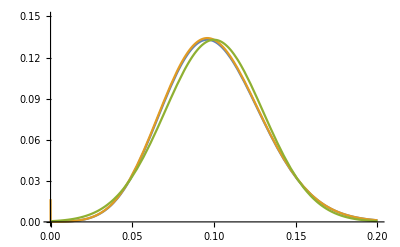

```mathematica
Plot[{Func2[0.1,α,100],Func[0.1,α,100],Func4[0.1,α,100]},{α,0,0.2},PlotRange->{0,0.15}]
```

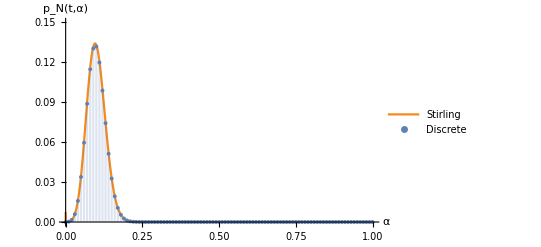

```mathematica
Show[Plot[Func[0.1,α,100],{α,0,1},PlotRange->{0,0.15},AxesLabel->{"α","p_N(t,α)"},PlotStyle->ColorData[106,"ColorList"],PlotLegends->Placed[{"Stirling"},{0.81,0.8}]],DiscretePlot[Func3[0.1,α,100],{α,0,1,0.01},PlotMarkers->{Automatic, Tiny},PlotLegends->Placed[{"Discrete"},{0.835,0.9}]]]
```

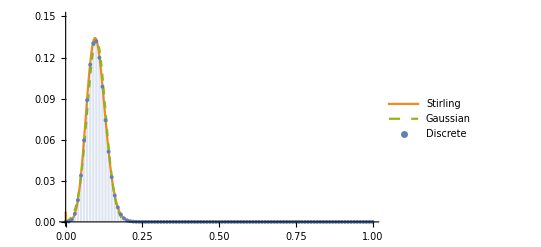

```mathematica
Show[Plot[Func[0.1,α,100],{α,0,1},PlotRange->{0,0.15},PlotStyle->ColorData[106,"ColorList"],PlotLegends->Placed[{"Stirling"},{0.81,0.8}]],Plot[Func4[0.1,α,100],{α,0,1},PlotRange->{0,0.15},AxesLabel->{"α","p_N(t,α)"},PlotStyle->{Dashed,ColorData[102,"ColorList"]},PlotLegends->Placed[{"Gaussian"},{0.8,0.7}]],DiscretePlot[Func3[0.1,α,100],{α,0,1,0.01},PlotRange->{0,0.15},PlotMarkers->{Automatic, Tiny},PlotLegends->Placed[{"Discrete"},{0.835,0.9}]]]
```

```mathematica
Func5[N_]:=PDF[BinomialDistribution[N,0.5],0.5N]
```

```mathematica
Func6[M_]:=N[Sqrt[2/(Pi M)]]
```

```mathematica
Func5[100]
```

0.0795892

```mathematica
Func6[100]
```

0.0797885

```mathematica
Su[u_]:=N(Log[1+2Cosh[u]] -2u Sinh[u]/(1+2Cosh[u]))
```

```mathematica
Eu[u_]:=-2N ϵ Sinh[u]/(1+2Cosh[u])
```

```mathematica
Limit[Su[u],u->Infinity]
```

0

```mathematica
Limit[Eu[u],u->Infinity]
```

-N ϵ

```mathematica
Series[Su[u],{u,0,2}]
```

N Log[3]-(N u^2)/3+O[u]^3

```mathematica
D[Su[u],u]
```

```mathematica
Simplify[N (-(2 u Cosh[u])/(1+2 Cosh[u])+(4 u Sinh[u]^2)/(1+2 Cosh[u])^2)]
```

-(2 N u (2+Cosh[u]))/(1+2 Cosh[u])^2

```mathematica
Simplify[D[Su[u],u]]
```

-(2 N u (2+Cosh[u]))/(1+2 Cosh[u])^2

```mathematica
Simplify[D[D[Su[u],u],u]]
```

-(2 N (3+5 Cosh[u]+Cosh[2 u]-7 u Sinh[u]-u Sinh[2 u]))/(1+2 Cosh[u])^3

```mathematica
Series[Eu[u],{u,0,3}]
```

-2/3 (N ϵ) u+1/9 N ϵ u^3+O[u]^4

```mathematica
Eu[0]
```

0

```mathematica
Simplify[D[Eu[u], u]]
```

-(2 N ϵ (2+Cosh[u]))/(1+2 Cosh[u])^2

```mathematica
Simplify[D[D[Eu[u], u],u]]
```

(2 N ϵ (7+2 Cosh[u]) Sinh[u])/(1+2 Cosh[u])^3

```mathematica
Simplify[D[D[D[Eu[u], u],u],u]]
```

-(2 N ϵ (-28-12 Cosh[u]+12 Cosh[2 u]+Cosh[3 u]))/(1+2 Cosh[u])^4

```mathematica
Limit[Su[u], u->Infinity]
```

0

```mathematica
Limit[Eu[u], u->Infinity]
```

-N ϵ

```mathematica
Sv[v_]:=N(Log[1+2Cosh[1/v]] -2/v Sinh[1/v]/(1+2Cosh[1/v]))
```

```mathematica
Ev[v_]:=-2N ϵ Sinh[1/v]/(1+2Cosh[1/v])
```

```mathematica
Series[Sv[v],{v,0,5}]
```

N Log[1+2 Cosh[1/v+O[v]^6]]+((-(2 N)/v+O[v]^6) Sinh[1/v+O[v]^6])/(1+2 Cosh[1/v+O[v]^6])

```mathematica
Simplify[D[Sv[v],v]]
```

(2 N (2+Cosh[1/v]))/(v^3 (1+2 Cosh[1/v])^2)

```mathematica
Simplify[D[D[Sv[v],v],v]]
```

-(2 N (9 v+15 v Cosh[1/v]+3 v Cosh[2/v]-7 Sinh[1/v]-Sinh[2/v]))/(v^5 (1+2 Cosh[1/v])^3)

```mathematica
Series[Ev[v],{v,0,5}]
```

-(2 N ϵ Sinh[1/v+O[v]^6])/(1+2 Cosh[1/v+O[v]^6])

```mathematica
Simplify[p^(3/2)/p^3]
```

1/p^(3/2)

```mathematica
D[Log[Factorial[N](V/h^3(m/(2Pi β))^(3/2))^N],β]
```

-(3 N)/(2 β)

```mathematica
Binomial[6,2]
```

15

```mathematica
Binomial[6,1]
```

6